```mathematica
DSolve[{y''[x]+y[x]*x^2m^4==0},y[x],x]
```

{{y[x]→C[1] ParabolicCylinderD[-1/2,(-1)^(1/4) √2 m x]+C[2] ParabolicCylinderD[-1/2,(-1)^(3/4) √2 m x]}}

```mathematica
ParabolicCylinderD[-1/2,0]
```

(√π)/(2^(1/4) Gamma[3/4])

```mathematica
ParabolicCylinderD[-1/2,0]
```

(√π)/(2^(1/4) Gamma[3/4])

```mathematica
D[ParabolicCylinderD[-1/2,x],x]
```

1/2 x ParabolicCylinderD[-1/2,x]-ParabolicCylinderD[1/2,x]

```mathematica
Sol[x_,m_]:=ParabolicCylinderD[-1/2,m(1+I)x]-ParabolicCylinder[-1/2,m(-1+I)x]
```

```mathematica
FullSimplify[D[Sol[x],x]/.{x->1}]
```

Sol'[1]

```mathematica
der[m_]:=ⅈ m (m ParabolicCylinderD[-1/2,(1+ⅈ) m]-(1-ⅈ) (ParabolicCylinderD[1/2,(1+ⅈ) m]+ⅈ Derivative[0,1][ParabolicCylinder][-1/2,(-1+ⅈ) m]))
```

```mathematica
NSolve[der[m]==0,m]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m→0.}}

```mathematica
FindRoot[der[m]==0,{m,0.1}]
```

FindRoot::nlnum: The function value {(0.`  + 0.1` ⅈ) ((0.11581335375890106`  - 0.0058136541018157` ⅈ) - (1.`  - 1.` ⅈ) ((0.6423699994229543`  + 0.054797137183475245` ⅈ) + (0.`  + 1.` ⅈ) SuperscriptBox[ is not a list of numbers with dimensions {1} at {m} = {0.1`}.

FindRoot[der[m]==0,{m,0.1}]

```mathematica
N[FullSimplify[der[0.1]]]
```

(-0.0581759-0.0581354 ⅈ)+(0.1-0.1 ⅈ) ParabolicCylinder^(0,1)[-0.5,-0.1+0.1 ⅈ]

```mathematica
N[Derivative[0,1][ParabolicCylinder][-0.5,0.1]]
```

ParabolicCylinder^(0,1)[-0.5,0.1]

```mathematica
N[BesselJ[-1/4,1]]
```

0.669385

```mathematica
N[BesselJ[1/4,1]]
```

0.752231

```mathematica
fun1[x_]:=2^{-5/4}*Sqrt[π x]*(BesselJ[-1/4,x^2/4]+BesselJ[1/4,x^2/4])
```

```mathematica
fun2[x_]:=2^{-5/4}*Sqrt[π x]*(BesselJ[-1/4,x^2/4]-BesselJ[1/4,x^2/4])
```

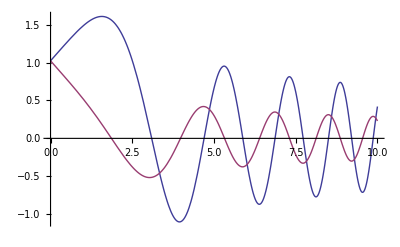

```mathematica
Plot[{fun1[x],fun2[x]},{x,0,10}]
```

```mathematica
funm1[x_]:=1/2 √π √(m x) (BesselJ[-1/4,(m^2 x^2)/2]+BesselJ[1/4,(m^2 x^2)/2])
```

```mathematica
funm2[x_]:=1/2 √π √(m x) (BesselJ[-1/4,(m^2 x^2)/2]-BesselJ[1/4,(m^2 x^2)/2])
```

```mathematica
funderm1=FullSimplify[D[funm1[x],x]]
```

1/2 m √π (m x)^(3/2) (BesselJ[-3/4,(m^2 x^2)/2]-BesselJ[3/4,(m^2 x^2)/2])

```mathematica
funderm2=FullSimplify[D[funm2[x],x]]
```

-1/2 m √π (m x)^(3/2) (BesselJ[-3/4,(m^2 x^2)/2]+BesselJ[3/4,(m^2 x^2)/2])

```mathematica
NSolve[funm1[0]*funderm2[1]-funm2[0]*funderm1[1]==0,m]
```

∞::indet: Indeterminate expression 0 √π ComplexInfinity encountered.

{{}}

```mathematica
Limit[funm1[x],x->0]
```

((m^2)^(3/4) √(π/2))/(m^(3/2) Gamma[3/4])

```mathematica
Limit[funm2[x],x->0]
```

((m^2)^(3/4) √(π/2))/(m^(3/2) Gamma[3/4])

```mathematica
FullSimplify[funderm1/.{x->1}]
```

1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]-BesselJ[3/4,m^2/2])

```mathematica
FullSimplify[funderm2/.{x->1}]
```

-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]+BesselJ[3/4,m^2/2])

```mathematica
FullSimplify[-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]+BesselJ[3/4,m^2/2])-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]-BesselJ[3/4,m^2/2])==0]
```

m^(5/2) BesselJ[-3/4,m^2/2]==0

```mathematica
BesselJZero[-3/4,10]
```

BesselJZero[-3/4,10]

```mathematica
N[BesselJZero[-3/4,1]]
```

1.05851

```mathematica
Zeros=Table[N[Sqrt[2BesselJZero[-3/4,i]],10],{i,1,100}]
```

{1.454997085,2.927133004,3.857578101,4.601777732,5.240824067,5.809787864,6.327694301,6.806248002,7.25326169,7.6742593,8.073317953,8.453548974,8.817390869,9.166797024,9.503360989,9.828402986,10.14303138,10.44818742,10.74467855,11.0332036,11.31437223,11.58872006,11.8567207,12.11879537,12.37532065,12.62663484,12.8730432,13.11482231,13.3522237,13.58547689,13.81479204,14.04036213,14.26236488,14.48096438,14.69631251,14.90855018,15.11780841,15.32420926,15.5278667,15.72888729,15.92737088,16.12341118,16.31709625,16.508509,16.69772758,16.88482577,17.06987328,17.25293611,17.43407678,17.61335459,17.79082587,17.96654416,18.14056039,18.31292309,18.48367852,18.65287083,18.82054216,18.98673282,19.15148136,19.31482468,19.47679813,19.63743561,19.79676966,19.95483148,20.11165108,20.26725729,20.42167785,20.57493946,20.72706782,20.87808772,21.02802303,21.17689679,21.32473123,21.47154783,21.61736732,21.76220974,21.90609448,22.04904029,22.1910653,22.3321871,22.47242269,22.61178856,22.7503007,22.88797461,23.02482533,23.16086744,23.29611511,23.4305821,23.56428178,23.69722713,23.82943078,23.96090501,24.09166175,24.22171263,24.35106896,24.47974174,24.60774171,24.7350793,24.86176469,24.98780781}

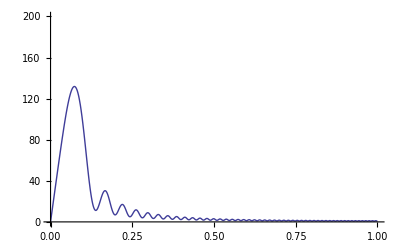

```mathematica
Plot[Sum[(funm1[x]/.{m->Zeros[[i]]})-(funm2[x]/.{m->Zeros[[i]]}),{i,1,100}],{x,0,1},PlotRange->{{0,1},{0,200}}]
```

## Testing solution

```mathematica
test=Sqrt[π x]*BesselJ[-1/4,x^2/4]
```

√π √x BesselJ[-1/4,x^2/4]

```mathematica
FullSimplify[D[test,{x,2}]]
```

-1/4 √π x^(5/2) BesselJ[-1/4,x^2/4]

```mathematica
FullSimplify[D[test,{x,2}]+x^2/4*test]
```

0

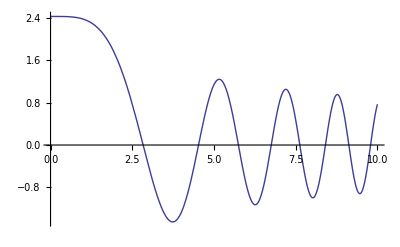

```mathematica
Plot[test,{x,0,10}]
```

```mathematica
sol1=Sqrt[m x]*BesselJ[-1/4,m^2 x^2/2]
```

√(m x) BesselJ[-1/4,(m^2 x^2)/2]

```mathematica
sol1
```

√x BesselJ[-1/3,2/3 m x^(3/2)]

```mathematica
sol2=Sqrt[m x]*BesselJ[1/4,m^2 x^2/2]
```

√(m x) BesselJ[1/4,(m^2 x^2)/2]

```mathematica
Limit[sol1,x->0]
```

(√2 (m^2)^(3/4))/(m^(3/2) Gamma[3/4])

```mathematica
Limit[sol2,x->0]
```

0

```mathematica
sol1
```

√(m x) BesselJ[-1/4,(m^2 x^2)/2]

```mathematica
dersol1=FullSimplify[D[sol1,x]]
```

-m (m x)^(3/2) BesselJ[3/4,(m^2 x^2)/2]

```mathematica
dersol2=FullSimplify[D[sol2,x]]
```

m (m x)^(3/2) BesselJ[-3/4,(m^2 x^2)/2]

```mathematica
Limit[dersol1,x->1]
```

-m^(5/2) BesselJ[3/4,m^2/2]

```mathematica
Limit[dersol2,x->1]
```

m^(5/2) BesselJ[-3/4,m^2/2]

```mathematica
Zerostrue=Table[Sqrt[2BesselJZero[-3/4,i]],{i,1,80}];
```

```mathematica
coeffs=Table[BesselJZero[-3/4,i],{i,1,200}];
```

```mathematica
Zeros=Table[N[Sqrt[2BesselJZero[-3/4,i]],10],{i,1,160}]
```

{1.454997085,2.927133004,3.857578101,4.601777732,5.240824067,5.809787864,6.327694301,6.806248002,7.25326169,7.6742593,8.073317953,8.453548974,8.817390869,9.166797024,9.503360989,9.828402986,10.14303138,10.44818742,10.74467855,11.0332036,11.31437223,11.58872006,11.8567207,12.11879537,12.37532065,12.62663484,12.8730432,13.11482231,13.3522237,13.58547689,13.81479204,14.04036213,14.26236488,14.48096438,14.69631251,14.90855018,15.11780841,15.32420926,15.5278667,15.72888729,15.92737088,16.12341118,16.31709625,16.508509,16.69772758,16.88482577,17.06987328,17.25293611,17.43407678,17.61335459,17.79082587,17.96654416,18.14056039,18.31292309,18.48367852,18.65287083,18.82054216,18.98673282,19.15148136,19.31482468,19.47679813,19.63743561,19.79676966,19.95483148,20.11165108,20.26725729,20.42167785,20.57493946,20.72706782,20.87808772,21.02802303,21.17689679,21.32473123,21.47154783,21.61736732,21.76220974,21.90609448,22.04904029,22.1910653,22.3321871,22.47242269,22.61178856,22.7503007,22.88797461,23.02482533,23.16086744,23.29611511,23.4305821,23.56428178,23.69722713,23.82943078,23.96090501,24.09166175,24.22171263,24.35106896,24.47974174,24.60774171,24.7350793,24.86176469,24.98780781,25.11321832,25.23800565,25.36217901,25.48574737,25.60871948,25.7311039,25.85290896,25.97414283,26.09481347,26.21492864,26.33449595,26.45352284,26.57201655,26.6899842,26.80743273,26.92436894,27.04079946,27.1567308,27.27216934,27.38712129,27.50159277,27.61558975,27.72911807,27.84218348,27.95479159,28.0669479,28.17865781,28.28992661,28.40075948,28.5111615,28.62113767,28.73069287,28.83983189,28.94855946,29.05688017,29.16479858,29.27231912,29.37944617,29.48618402,29.59253687,29.69850887,29.80410407,29.90932646,30.01417998,30.11866846,30.2227957,30.32656541,30.42998126,30.53304684,30.63576569,30.73814128,30.84017702,30.94187629,31.04324239,31.14427857,31.24498803,31.34537392,31.44543935,31.54518735,31.64462094}

```mathematica
1.45499708549819386722507026854180579346`10.,2.92713300440027766553121136094888110735`10.,3.8575781013492938200342434118812546441`10.,4.60177773228129985324241798621793597148`10.,5.24082406699070314354952418816449605517`10.,5.80978786426398906487468774457944491812`10.,6.32769430108396681532057061373337375445`10.,6.8062480022514212669586769504065468988`10.,7.25326168965686308822824791463505009483`10.,7.6742592995607184149250788121278225534`10.,8.07331795319108946335626947213305371378`10.,8.45354897437340233163926840148873400306`10.,8.81739086884080680472896916336389339722`10.,9.16679702363228751221979864959553140746`10.,9.50336098897760887069148869968298949199`10.,9.82840298647447126437751319761265707777`10.,10.14303137712219911244514916412671544951`10.,10.44818741811621983414432659838862125807`10.,10.74467854808127573053205335964669225223`10.,11.03320360258297538892991564331548075855`10.,11.31437222998145142057443770168774860219`10.,11.58872005940677119103217820431909528765`10.,11.85672070452047449321754322768063874146`10.,12.11879537438111167446084673341581712359`10.,12.37532064988645588833414500384166974648`10.,12.62663483645073127192279608364483685065`10.,12.8730431991488418101183117224826294002`10.,13.11482231162738863620077232279337810946`10.,13.35222369554359348133575969794532279845`10.,13.58547688707664934803393403887138075079`10.,13.81479203704230978691485194517723996389`10.,14.0403621284925403691860805796792028747`10.,14.2623648784142054972133104428159388272`10.,14.4809643768493324602515059590286238574`10.,14.69631250643745383397730190280670992963`10.,14.90855017729768053412230968849290743382`10.,15.11780840578937570988470787292523813834`10.,15.32420926061949995243758582398480085884`10.,15.52786669570596600871656820859722187773`10.,15.7288872859366536654040406731452138516`10.,15.9273708793136173631920062299682027691`10.,16.12341117681167755300451799359118160072`10.,16.31709624950989469369530608919286116217`10.,16.50850900109559236347854935232210542604`10.,16.69772758263279807557262678658274113287`10.,16.88482576548234240189867071924417329888`10.,17.0698732774215122579902242575503858456`10.,17.25293610630693319483410269200861091738`10.,17.43407677503112073131534139072114313752`10.,17.61335459102147480760264415427211297139`10.,17.79082587310469749719229172428528076748`10.,17.96654415819694343585843588062836815013`10.,18.14056038997006420349764940438806368648`10.,18.31292309137856038366383535925968134061`10.,18.48367852270329730273712784271426510892`10.,18.65287082657088177261838964015053009292`10.,18.82054216123703645850384614058496825444`10.,18.98673282327435071906554950975388778683`10.,19.15148136067609592105538219021147335869`10.,19.31482467727557424266429445652771548091`10.,19.47679812928237338488715497506428607718`10.,19.63743561465094432179652946866365109956`10.,19.79676965592142972660408702565954850112`10.,19.95483147710622580687699207508067817164`10.,20.1116510751371510811081913728251719114`10.,20.26725728633629104179428517626838796877`10.,20.42167784832770592539536914201674076594`10.,20.5749394577664739838553947225769077593`10.,20.72706782422534501022699390743200749406`10.,20.87808772054703867991961754439254908311`10.,21.02802302994145620306095998066847616749`10.,21.17689679008136355778581681928277317273`10.,21.32473123442708740654118303228698174865`10.,21.47154783099012537957908642158269803669`10.,21.61736731872703613437482639643069462277`10.,21.76220974173830183110201170131191655663`10.,21.90609448143183688097899306297480577485`10.,22.0490402867972684906486490578908342351`10.,22.19106530292487557569193393086240056928`10.,22.33218709789200145155224658654248859863`10.,22.47242268812972763181726728233480068426`10.,22.61178856237350107116482179887720435212`10.,22.75030070429314808911143247007435463568`10.,22.88797461389019898535743216669742834062`10.,23.02482532774361176686908350481669578922`10.,23.16086743817875377107897094013951992889`10.,23.29611511142881612007056991591400670695`10.,23.43058210485264430911534250581744912669`10.,23.56428178326822106049067042363678474115`10.,23.69722713445669222196499462428128809258`10.,23.82943078388784484123560074037466926473`10.,23.96090500871429448226506215187209941985`10.,24.09166175107828578483607659944185750049`10.,24.22171263077192876006624179524327743237`10.,24.35106895728885870286413371602770640852`10.,24.47974174130269770440759596094085980563`10.,24.60774170560529058502534730748486421888`10.,24.73507929553546962640942278460409394305`10.,24.86176468892705450126529037039701151511`10.,24.98780780560290158433514050182926229463`10.,25.11321831644006708870055811559405011212`10.,25.23800565202952916807855725233848557165`10.,25.36217901095241434764955105803052194794`10.,25.48574736769328349128365881159583403571`10.,25.60871948020974298826286481975975821267`10.,25.73110389717644977090884369535145447412`10.,25.85290896492046671466441961895419977548`10.,25.97414283406389114600188817002274285412`10.,26.09481346588871741131460938622563226671`10.,26.21492863843799910251461835808144532308`10.,26.33449595236654244200346861227048588322`10.,26.45352283655358479297050162584261891475`10.,26.57201655348918697331695241490058544311`10.,26.68998420444539106900228677122542365513`10.,26.80743273444256315115350431279997534856`10.,26.92436893702074938634192144279007313002`10.,27.04079945882532144885899301531481996968`10.,27.15673080401567010330138314407973778928`10.,27.27216933850522175671071533349314030512`10.,27.38712129404059931904444842046619226734`10.,27.5015927721273236836935924258084318931`10.,27.61558974780905354225731176234972335349`10.,27.7291180733069872325213158703418891891`10.,27.84218348152569918138829195005926719402`10.,27.95479158943135367217217459578099206443`10.,28.06694790130792868493048549539313948149`10.,28.17865781189679108601986330122701795418`10.,28.28992660942469023626614819841869888214`10.,28.40075947852497899599227553112094158799`10.,28.51116150305662806454610751360670020052`10.,28.62113766882537061488637648812395120886`10.,28.73069286621109835498093694749057922709`10.,28.83983189270542661807516764707431009937`10.,28.94855945536315406496103915669137916186`10.,29.0568801731711613409334377673415823046`10.,29.16479857933812188755478470256750080465`10.,29.27231912350823643173581130305598484097`10.,29.37944617390204987306787317871788072344`10.,29.48618401938726481655462124120669710125`10.,29.59253687148232934120849531844604066321`10.,29.69850886629544727947065323370919097601`10.,29.80410406640153686430690657788455184085`10.,29.90932646265954766612311748559774855157`10.,30.01417997597243590390627603971350150613`10.,30.11866845899199411336949914690532327191`10.,30.22279569777063245220418800300579966128`10.,30.32656541336211530366113731323828860625`10.,30.42998126337316800985656774510794595015`10.,30.53304684346778424965974281784788344284`10.,30.63576568882598451462550996210811760772`10.,30.73814127555870008843862044749237208531`10.,30.84017702208038467423650413525089107265`10.,30.94187629044088712766532761964247197981`10.,31.04324238761805344250874245193788967589`10.,31.14427856677246401343051602820994092765`10.,31.24498802846565309148851505340619403559`10.,31.34537392184310108800767554807196747595`10.,31.44543934578323681652762544616436194505`10.,31.54518735001363574556992207115040025218`10.,31.64462093619555173030629520550814059172`10.
```

```mathematica
Table[N[BesselJZero[-3/4,i],10],{i,1,10}]
```

{1.058508259,4.284053813,7.440454404,10.58817915,13.73311845,16.87681751,20.01985758,23.16250593,26.30490257,29.4471279}

```mathematica
N[BesselJ[3/4,BesselJZero[-3/4,3]]]
```

0.207121

```mathematica
N[BesselJ[1/4,BesselJZero[-3/4,1]]]
```

0.742897

```mathematica
sol2
```

√(m x) BesselJ[1/4,(m^2 x^2)/2]

```mathematica
sol2m=√x BesselJ[1/4,(m^2 x^2)/2]
```

√x BesselJ[1/4,(m^2 x^2)/2]

```mathematica
Plot[Sum[(sol2m/.{m->Zerostrue[[i]]}),{i,1,10}],{x,0,1},PlotRange->{{0,1},{0,100}}]
```

$Aborted

```mathematica
NIntegrate[x^3 BesselJ[1/4,x^2/2*Zerostrue[[2]]^2]*BesselJ[1/4,x^2/2*Zerostrue[[2]]^2],{x,0,1}]
```

0.0368546

```mathematica
wmcubic=Table[NIntegrate[x^3 BesselJ[1/4,x^2/2*Zeros[[i]]^2]^2,{x,0,1}],{i,81,160}]
```

NIntegrate::precw: The precision of the argument function (x^3 BesselJ[1/4, 252.50489073698386684851928257492913473823`9.698970004336022 x^2]^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (x^3 BesselJ[1/4, 255.64649099474254117092921709370046845072`9.698970004336022 x^2]^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (x^3 BesselJ[1/4, 258.78809106788065498613104475945589137652`9.698970004336022 x^2]^2) is less than WorkingPrecision (MachinePrecision).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{0.000630303,0.000622557,0.000615,0.000607623,0.000600422,0.000593389,0.000586519,0.000579806,0.000573246,0.000566832,0.00056056,0.000554425,0.000548423,0.00054255,0.000536801,0.000531173,0.000525661,0.000520263,0.000514974,0.000509792,0.000504713,0.000499735,0.000494853,0.000490066,0.000485371,0.000480765,0.000476245,0.00047181,0.000467456,0.000463183,0.000458986,0.000454865,0.000450817,0.000446841,0.000442934,0.000439095,0.000435322,0.000431613,0.000427967,0.000424382,0.000420856,0.000417389,0.000413978,0.000410623,0.000407321,0.000404073,0.000400875,0.000397728,0.00039463,0.000391579,0.000388576,0.000385618,0.000382705,0.000379836,0.000377009,0.000374224,0.00037148,0.000368776,0.000366111,0.000363484,0.000360895,0.000358342,0.000355825,0.000353343,0.000350896,0.000348482,0.000346101,0.000343753,0.000341436,0.00033915,0.000336895,0.000334669,0.000332473,0.000330305,0.000328166,0.000326054,0.000323969,0.00032191,0.000319877,0.00031787}

```mathematica
wmcubicpredefined={0.13797406599320738,0.036854581143239175,0.02133155594370827,0.015010686087355087,0.011579602879061325,0.009425240459319681,0.00794676552988761,0.006869235708429393,0.006049027438296182,0.005403797343711836,0.004882949141705082,0.0044536787382349384,0.0040937854185415555,0.0037877079495512375,0.0035242151877391964,0.003294997916730558,0.0030937766542952425,0.002915717555439377,0.0027570390413366227,0.0026147402465559653,0.0024864094328322945,0.002370086181472648,0.002264160539779118,0.0021672980550348627,0.0020783832616715044,0.0019964765310819576,0.0019207807375925753,0.001850615230525651,0.001785395309967969,0.0017246158947239064,0.0016678384163521522,0.0016146802195225812,0.0015648059267859933,0.0015179203557653368,0.0014737626725206412,0.0014321015367415484,0.0013927310476398757,0.0013554673405968029,0.00132014571598235,0.0012866182056656857,0.0012547515008308823,0.0012244251805145821,0.0011955301909566858,0.0011679675352164775,0.001141647140020983,0.0011164868724411468,0.001092411683789792,0.0010693528619443273,0.0010472473764049522,0.0010260373029400856,0.001005669316760948,0.0009860942448871525,0.0009672666697926882,0.0009491445776069171,0.0009316890451347559,0.0009148639607888969,0.000898635775223389,0.0008829732780440975,0.0008678473974712466,0.0008532310202445551,0.000839098829416329,0.0008254271580562615,0.0008121938569205483,0.0007993781747559135,0.0007869606497074265,0.0007749230107130705,0.0007632480877511553,0.0007519197302406965,0.0007409227323453307,0.0007302427650298862,0.0007198663136691806,0.0007097806209968215,0.0006999736348672356,0.0006904339601143648,0.0006811508144305624,0.0006721139877036992,0.0006633138045573109,0.0006547410897960503,0.0006463871364960805,0.0006382436765076748,0.0006303028531598466,0.0006225571959772052,0.0006149995972390405,0.00060762329023299,0.0006004218290146798,0.0005933890696697541,0.0005865191527910231,0.0005798064872363093,0.0005732457349049316,0.0005668317966193273,0.0005605597988617798,0.000554425081500312,0.000548423186165646,0.0005425498454906621,0.0005368009729481291,0.0005311726534411112,0.0005256611343459384,0.0005202628171764819,0.0005149742497774396,0.000509792118961795,0.0005047132435614256,0.0004997345679090261,0.0004948531557746551,0.0004900661844907577,0.00048537093960920554,0.00048076480969575636,0.0004762452815198213,0.00047180993548151946,0.0004674564412607595,0.00046318255379765045,0.0004589861093689904,0.00045486502196710586,0.00045081727983601596,0.0004468409421967647,0.00044293413614472334,0.00043909505370775154,0.00043532194905709584,0.0004316131358594908,0.0004279669847644897,0.00042438192101768214,0.00042085642219294103,0.000417389016036788,0.00041397827841843323,0.00041062283137950596,0.0004073213412778911,0.0004040725170212972,0.0004008751083791981,0.00039772790438793656,0.0003946297318123248,0.000391579453691969,0.000388575967949311,0.0003856182060619201,0.000382705131795076,0.0003798357399915421,0.00037700905541481736,0.0003742241316443967,0.00037148005001910067,0.0003687759186267475,0.0003661108713376293,0.0003634840668795648,0.0003608946879525167,0.00035834194038075984,0.0003558250523007927,0.00035334327338323315,0.0003508958740870435,0.00034848214494454037,0.0003461013958757237,0.0003437529555304854,0.00034143617065746486,0.0003391504054982293,0.00033689504120561653,0.0003346694752851603,0.0003324731210584933,0.000330305407147744,0.00032816577697996523,0.00032605368831072697,0.0003239686127659561,0.0003219100354012626,0.00031987745427795427,0.00031787038005491955}
```

{0.137974,0.0368546,0.0213316,0.0150107,0.0115796,0.00942524,0.00794677,0.00686924,0.00604903,0.0054038,0.00488295,0.00445368,0.00409379,0.00378771,0.00352422,0.003295,0.00309378,0.00291572,0.00275704,0.00261474,0.00248641,0.00237009,0.00226416,0.0021673,0.00207838,0.00199648,0.00192078,0.00185062,0.0017854,0.00172462,0.00166784,0.00161468,0.00156481,0.00151792,0.00147376,0.0014321,0.00139273,0.00135547,0.00132015,0.00128662,0.00125475,0.00122443,0.00119553,0.00116797,0.00114165,0.00111649,0.00109241,0.00106935,0.00104725,0.00102604,0.00100567,0.000986094,0.000967267,0.000949145,0.000931689,0.000914864,0.000898636,0.000882973,0.000867847,0.000853231,0.000839099,0.000825427,0.000812194,0.000799378,0.000786961,0.000774923,0.000763248,0.00075192,0.000740923,0.000730243,0.000719866,0.000709781,0.000699974,0.000690434,0.000681151,0.000672114,0.000663314,0.000654741,0.000646387,0.000638244,0.000630303,0.000622557,0.000615,0.000607623,0.000600422,0.000593389,0.000586519,0.000579806,0.000573246,0.000566832,0.00056056,0.000554425,0.000548423,0.00054255,0.000536801,0.000531173,0.000525661,0.000520263,0.000514974,0.000509792,0.000504713,0.000499735,0.000494853,0.000490066,0.000485371,0.000480765,0.000476245,0.00047181,0.000467456,0.000463183,0.000458986,0.000454865,0.000450817,0.000446841,0.000442934,0.000439095,0.000435322,0.000431613,0.000427967,0.000424382,0.000420856,0.000417389,0.000413978,0.000410623,0.000407321,0.000404073,0.000400875,0.000397728,0.00039463,0.000391579,0.000388576,0.000385618,0.000382705,0.000379836,0.000377009,0.000374224,0.00037148,0.000368776,0.000366111,0.000363484,0.000360895,0.000358342,0.000355825,0.000353343,0.000350896,0.000348482,0.000346101,0.000343753,0.000341436,0.00033915,0.000336895,0.000334669,0.000332473,0.000330305,0.000328166,0.000326054,0.000323969,0.00032191,0.000319877,0.00031787}

```mathematica
wmfivetwo=Table[NIntegrate[x^(5/2) BesselJ[1/4,x^2/2*Zeros[[i]]^2],{x,0,1}],{i,81,160}]
```

NIntegrate::precw: The precision of the argument function (x^5/2 BesselJ[1/4, 252.50489073698386684851928257492913473823`9.698970004336022 x^2]) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (x^5/2 BesselJ[1/4, 255.64649099474254117092921709370046845072`9.698970004336022 x^2]) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (x^5/2 BesselJ[1/4, 258.78809106788065498613104475945589137652`9.698970004336022 x^2]) is less than WorkingPrecision (MachinePrecision).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{0.0000145007,0.0000141903,0.0000138902,0.0000136,0.0000133192,0.0000130473,0.0000127841,0.0000125292,0.0000122821,0.0000120427,0.0000118104,0.0000115852,0.0000113666,0.0000111544,0.0000109484,0.0000107483,0.0000105539,0.000010365,0.0000101813,0.0000100027,9.82892×10^-6,9.65987×10^-6,9.49535×10^-6,9.33519×10^-6,9.17923×10^-6,9.02733×10^-6,8.87935×10^-6,8.73514×10^-6,8.59457×10^-6,8.45753×10^-6,8.32389×10^-6,8.19354×10^-6,8.06637×10^-6,7.94227×10^-6,7.82115×10^-6,7.70291×10^-6,7.58745×10^-6,7.47468×10^-6,7.36453×10^-6,7.25691×10^-6,7.15174×10^-6,7.04894×10^-6,6.94845×10^-6,6.85019×10^-6,6.75409×10^-6,6.6601×10^-6,6.56815×10^-6,6.47817×10^-6,6.39012×10^-6,6.30394×10^-6,6.21956×10^-6,6.13695×10^-6,6.05605×10^-6,5.97681×10^-6,5.89919×10^-6,5.82314×10^-6,5.74862×10^-6,5.67559×10^-6,5.60401×10^-6,5.53384×10^-6,5.46503×10^-6,5.39756×10^-6,5.33139×10^-6,5.26649×10^-6,5.20282×10^-6,5.14035×10^-6,5.07905×10^-6,5.01889×10^-6,4.95985×10^-6,4.90189×10^-6,4.84498×10^-6,4.78911×10^-6,4.73424×10^-6,4.68036×10^-6,4.62743×10^-6,4.57544×10^-6,4.52436×10^-6,4.47417×10^-6,4.42484×10^-6,4.37637×10^-6}

```mathematica
wmfivetwopredefined={0.20996479709362217,0.018180897590318785,0.006919303361557072,0.0037318500468507265,0.0023673658890243144,0.0016504522182779553,0.0012240656323313512,0.0009483894730813764,0.0007590968780885121,0.0006230691899630487,0.000521773141559365,0.0004441474396258039,0.00038324243624026397,0.00033450473194280715,0.0002948449039830018,0.0002621039555673866,0.0002347343932804438,0.00021160239472918784,0.00019186109713872825,0.00017486713895424112,0.00016012432055124612,0.00014724473213250115,0.0001359214046973261,0.00012590872750600792,0.00011700820222555297,0.0001090579288501799,0.00010192474302362525,0.00009549826478267914,0.00008968634379190777,0.00008441153749062422,0.00007960836196536182,0.00007522112702512196,0.00007120221729922205,0.00006751071698186362,0.0000641113016165315,0.000060973339051508034,0.00005807015547318643,0.00005537843263812609,0.00005287771007323228,0.00005054997178480274,0.000048379301408858354,0.00004635159310216252,0.00004445430807096168,0.00004267626865559752,0.00004100748346843951,0.00003943899832564699,0.000037962768698096496,0.000036571550189571094,0.00003525880417636117,0.00003401861624793521,0.00003284562549298673,0.00003173496300815666,0.000030682198273720266,0.00002968329226266342,0.0000287345563299556,0.000027832616078876215,0.0000269743795242561,0.00002615700897675555,0.00002537789615694936,0.000024634640120406708,0.00002392502763531586,0.000023247015704908107,0.000022598715969558762,0.00002197838076039508,0.000021384390606644113,0.000020815243025254824,0.00002026954244416346,0.000019745991129333714,0.00001924338100264011,0.000018760586251353425,0.000018296556642761726,0.000017850311467667332,0.000017420934045730063,0.000017007566733802623,0.000016609406384810287,0.000016225700211394876,0.0000158557420132339,0.000015498868731945504,0.000015154457301158608,0.000014821921763302157,0.00001450071062731367,0.000014190304444456835,0.000013890213582018029,0.000013599976176311622,0.000013319156248667392,0.000013047341969944055,0.000012784144059735866,0.00001252919430900766,0.000012282144214937344,0.000012042663718404304,0.000011810440035547778,0.00001158517657507229,0.000011366591934418066,0.00001115441896833911,0.000010948403923597011,0.000010748305634853729,0.000010553894776504868,0.000010364953166337604,0.000010181273116649793,0.000010002656829307337,9.828915831386193*^-6,9.659870448208707*^-6,9.49534931097945*^-6,9.335188896470898*^-6,9.179233096398142*^-6,9.027332814266679*^-6,8.879345587644758*^-6,8.73513523417869*^-6,8.59457151961857*^-6,8.457529846050854*^-6,8.32389095943517*^-6,8.1935406745277*^-6,8.066369616458602*^-6,7.942272977545397*^-6,7.821150288441995*^-6,7.702905202654277*^-6,7.5874452934925025*^-6,7.47468186263942*^-6,7.364529759619492*^-6,7.256907211476081*^-6,7.151735661952972*^-6,7.048939619510668*^-6,6.94844651384123*^-6,6.850186560093698*^-6,6.754092630545741*^-6,6.660100132994738*^-6,6.568146895868383*^-6,6.478173059186307*^-6,6.390120971368812*^-6,6.3039350913559065*^-6,6.219561895780246*^-6,6.136949790954026*^-6,6.056049029226355*^-6,5.976811629690077*^-6,5.89919130273287*^-6,5.823143378440544*^-6,5.748624738477849*^-6,5.675593751315735*^-6,5.604010210652239*^-6,5.533835276712681*^-6,5.465031420482145*^-6,5.397562370506302*^-6,5.331393062241362*^-6,5.266489589791824*^-6,5.202819159859141*^-6,5.140350047878658*^-6,5.079051556127257*^-6,5.01889397376408*^-6,4.959848538681422*^-6,4.901887401087894*^-6,4.844983588703604*^-6,4.789110973507299*^-6,4.734244239954024*^-6,4.680358854602334*^-6,4.627431037040406*^-6,4.575437732101662*^-6,4.524356583247067*^-6,4.4741659071123195*^-6,4.424844669102156*^-6,4.376372460064756*^-6}
```

{0.209965,0.0181809,0.0069193,0.00373185,0.00236737,0.00165045,0.00122407,0.000948389,0.000759097,0.000623069,0.000521773,0.000444147,0.000383242,0.000334505,0.000294845,0.000262104,0.000234734,0.000211602,0.000191861,0.000174867,0.000160124,0.000147245,0.000135921,0.000125909,0.000117008,0.000109058,0.000101925,0.0000954983,0.0000896863,0.0000844115,0.0000796084,0.0000752211,0.0000712022,0.0000675107,0.0000641113,0.0000609733,0.0000580702,0.0000553784,0.0000528777,0.00005055,0.0000483793,0.0000463516,0.0000444543,0.0000426763,0.0000410075,0.000039439,0.0000379628,0.0000365716,0.0000352588,0.0000340186,0.0000328456,0.000031735,0.0000306822,0.0000296833,0.0000287346,0.0000278326,0.0000269744,0.000026157,0.0000253779,0.0000246346,0.000023925,0.000023247,0.0000225987,0.0000219784,0.0000213844,0.0000208152,0.0000202695,0.000019746,0.0000192434,0.0000187606,0.0000182966,0.0000178503,0.0000174209,0.0000170076,0.0000166094,0.0000162257,0.0000158557,0.0000154989,0.0000151545,0.0000148219,0.0000145007,0.0000141903,0.0000138902,0.0000136,0.0000133192,0.0000130473,0.0000127841,0.0000125292,0.0000122821,0.0000120427,0.0000118104,0.0000115852,0.0000113666,0.0000111544,0.0000109484,0.0000107483,0.0000105539,0.000010365,0.0000101813,0.0000100027,9.82892×10^-6,9.65987×10^-6,9.49535×10^-6,9.33519×10^-6,9.17923×10^-6,9.02733×10^-6,8.87935×10^-6,8.73514×10^-6,8.59457×10^-6,8.45753×10^-6,8.32389×10^-6,8.19354×10^-6,8.06637×10^-6,7.94227×10^-6,7.82115×10^-6,7.70291×10^-6,7.58745×10^-6,7.47468×10^-6,7.36453×10^-6,7.25691×10^-6,7.15174×10^-6,7.04894×10^-6,6.94845×10^-6,6.85019×10^-6,6.75409×10^-6,6.6601×10^-6,6.56815×10^-6,6.47817×10^-6,6.39012×10^-6,6.30394×10^-6,6.21956×10^-6,6.13695×10^-6,6.05605×10^-6,5.97681×10^-6,5.89919×10^-6,5.82314×10^-6,5.74862×10^-6,5.67559×10^-6,5.60401×10^-6,5.53384×10^-6,5.46503×10^-6,5.39756×10^-6,5.33139×10^-6,5.26649×10^-6,5.20282×10^-6,5.14035×10^-6,5.07905×10^-6,5.01889×10^-6,4.95985×10^-6,4.90189×10^-6,4.84498×10^-6,4.78911×10^-6,4.73424×10^-6,4.68036×10^-6,4.62743×10^-6,4.57544×10^-6,4.52436×10^-6,4.47417×10^-6,4.42484×10^-6,4.37637×10^-6}

```mathematica
coeffs=wmfivetwopredefined/wmcubicpredefined
```

{1.52177,0.493314,0.324369,0.248613,0.204443,0.17511,0.154033,0.138063,0.125491,0.115302,0.106856,0.099726,0.0936157,0.0883132,0.0836626,0.079546,0.0758731,0.072573,0.0695895,0.0668774,0.0643998,0.0621263,0.0600317,0.0580948,0.0562977,0.0546252,0.0530642,0.0516035,0.0502333,0.0489451,0.0477315,0.0465858,0.0455023,0.0444758,0.0435018,0.0425761,0.0416952,0.0408556,0.0400544,0.039289,0.0385569,0.0378558,0.0371838,0.0365389,0.0359196,0.0353242,0.0347513,0.0341997,0.0336681,0.0331553,0.0326605,0.0321825,0.0317205,0.0312737,0.0308414,0.0304227,0.030017,0.0296238,0.0292423,0.0288722,0.0285128,0.0281636,0.0278243,0.0274943,0.0271734,0.026861,0.026557,0.0262608,0.0259722,0.0256909,0.0254166,0.0251491,0.024888,0.0246332,0.0243843,0.0241413,0.0239038,0.0236718,0.0234449,0.023223,0.0230059,0.0227936,0.0225857,0.0223822,0.022183,0.0219878,0.0217966,0.0216093,0.0214256,0.0212456,0.021069,0.0208958,0.020726,0.0205593,0.0203956,0.0202351,0.0200774,0.0199225,0.0197705,0.0196211,0.0194743,0.01933,0.0191882,0.0190488,0.0189118,0.018777,0.0186445,0.0185141,0.0183858,0.0182596,0.0181354,0.0180131,0.0178928,0.0177743,0.0176576,0.0175427,0.0174295,0.017318,0.0172082,0.0170999,0.0169933,0.0168882,0.0167846,0.0166824,0.0165817,0.0164824,0.0163845,0.016288,0.0161927,0.0160987,0.016006,0.0159146,0.0158243,0.0157353,0.0156473,0.0155606,0.0154749,0.0153904,0.0153069,0.0152244,0.015143,0.0150626,0.0149832,0.0149047,0.0148272,0.0147507,0.014675,0.0146003,0.0145264,0.0144534,0.0143813,0.01431,0.0142395,0.0141698,0.0141009,0.0140328,0.0139654,0.0138988,0.0138329,0.0137678}

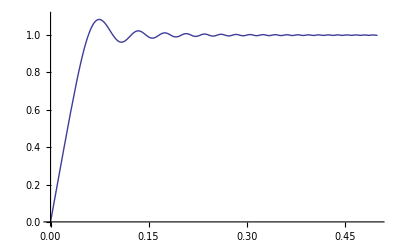

```mathematica
Plot[Sum[coeffs[[i]]Sqrt[x]*BesselJ[1/4,Zeros[[i]]^2*x^2/2],{i,1,160}],{x,0,0.5},PlotRange->{{0,0.5},{0,1.1}}]
```

```mathematica
N[Hypergeometric0F1[1/4,-1/4 BesselJZero[-3/4,2]^2]]
```

-2.65582×10^-15

```mathematica
Integrate[x^(5/2) BesselJ[1/4,x^2/2*Zerostrue[[2]]^2],{x,0,1}]
```

Limit::ztest1: Unable to decide whether numeric quantity Hypergeometric0F1[1/4, -1/4 BesselJZero[-3/4, 2]^2] is equal to zero. Assuming it is.

1/(2^(1/4) BesselJZero[-3/4,2]^(7/4) Gamma[1/4])

```mathematica
NIntegrate[x*BesselJ[1/4,x^2*coeffs[[1]]]*BesselJ[1/4,x^2*coeffs[[2]]],{x,0,1}]
```

0.0714686

```mathematica
N[Integrate[x*BesselJ[1/4,x^2/4]BesselJ[3/4,x^2/4],{x,0,1}]]
```

0.0371135

```mathematica
Integrate[x*BesselJ[1/4,x^2/4],{x,0,1}]
```

(4 2^(1/4) HypergeometricPFQ[{5/8},{5/4,13/8},-1/64])/(5 Gamma[1/4])

```mathematica
N[BesselJ[1/4,1]]
```

0.752231

## Linear Profile

```mathematica
DSolve[y''[x]+y[x]*x==0,y[x],x]
```

{{y[x]→AiryAi[(-1)^(1/3) x] C[1]+AiryBi[(-1)^(1/3) x] C[2]}}

```mathematica
sol1=Sqrt[x]BesselJ[-1/3,2/3m x^(3/2)]
```

√x BesselJ[-1/3,2/3 m x^(3/2)]

```mathematica
FullSimplify[D[sol1,{x,2}]+sol1*x*m^2]
```

0

```mathematica
sol2=Sqrt[x]*BesselJ[1/3,2/3*m*x^(3/2)]
```

√x BesselJ[1/3,2/3 m x^(3/2)]

```mathematica
FullSimplify[D[sol2,{x,2}]+sol2*x*m^2]
```

0

```mathematica
Limit[sol1,x->0]
```

3^(1/3)/(m^(1/3) Gamma[2/3])

```mathematica
Limit[sol2,x->0]
```

0

```mathematica
dersol1=FullSimplify[D[sol1,x]]
```

-m x BesselJ[2/3,2/3 m x^(3/2)]

```mathematica
dersol2=FullSimplify[D[sol2,x]]
```

m x BesselJ[-2/3,2/3 m x^(3/2)]

```mathematica
FullSimplify[Limit[dersol1,x->1]]
```

-(m^(5/3) Hypergeometric0F1Regularized[5/3,-m^2/9])/3^(2/3)

```mathematica
FullSimplify[Limit[dersol2,x->1]]
```

3^(2/3) m^(1/3) Hypergeometric0F1Regularized[1/3,-m^2/9]

```mathematica
Limit[dersol2,x->1]
```

1/2 m^(1/3) (-3 AiryAiPrime[-m^(2/3)]+√3 AiryBiPrime[-m^(2/3)])

```mathematica
Reduce[{Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m>0},m]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m>0},m]

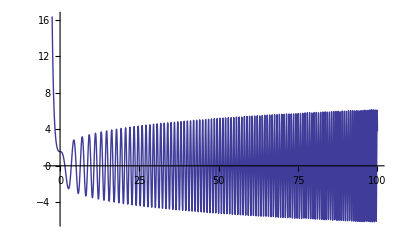

```mathematica
Plot[-3 AiryAiPrime[-x]+√3 AiryBiPrime[-x],{x,-3,100}]
```

```mathematica
Reduce[{-3 AiryAiPrime[-x]+√3 AiryBiPrime[-x]},x,Reals]
```

Reduce::naqs: And[-3 AiryAiPrime[-x] + √3 AiryBiPrime[-x]] is not a quantified system of equations and inequalities.

```mathematica
FindRoot[{-3 AiryAiPrime[-x]+√3 AiryBiPrime[-x]==0},{x,7}]
```

{x→17.4104}

```mathematica
Reduce[{Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m]

```mathematica
FullSimplify[Hypergeometric0F1[1/3,x]]
```

```mathematica
FunctionExpand[Hypergeometric0F1[a,-m^2/9]]
```

3^(-1+a) m^(1-a) BesselJ[-1+a,(2 m)/3] Gamma[a]

```mathematica
N[BesselJZero[-2/3,1]]
```

1.24305

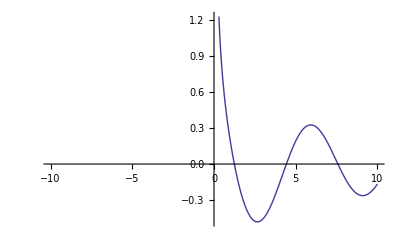

```mathematica
Plot[BesselJ[-2/3,x],{x,-10,10}]
```

```mathematica
FullSimplify[D[BesselJ[0,x^2]+2x^2BesselJ[0,x^2],{x,2}]]
```

-4 (-1+x^2+2 x^4) BesselJ[0,x^2]+2 (1-6 x^2) BesselJ[1,x^2]

```mathematica
oldtest=√x BesselJ[1/4,(m^2 x^2)/2]
```

√x BesselJ[1/4,(m^2 x^2)/2]

```mathematica
FullSimplify[D[oldtest,{x,2}]+m^4 x^2 oldtest]
```

0